```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
(* raster *)
R={Black,Thickness[0.01]};
R=Join[R,Table[Line[{{0,i},{8,i}}],{i,0,8}]];
R=Join[R,Table[Line[{{i,0},{i,8}}],{i,0,8}]];
(* triangle 1 *)
T1={Opacity[0.5],Red,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{0,5},{0,8},{8,8}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{0,i},{8/3(i-5),i}}],{i,6,8}],
Table[Line[{{i,5+3/8 i},{i,8}}],{i,0,7}]
};
T2={Opacity[0.5],Green,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{0,5},{8,5},{8,8}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{8/3(i-5),i},{8,i}}],{i,5,7}],
Table[Line[{{i,5},{i,5+3/8 i}}],{i,0,8}]
};
T3={Opacity[0.5],Blue,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{0,0},{5,0},{3,5},{0,5}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{0,i},{5-2/5 i,i}}],{i,1,5}],
Table[Line[{{i,0},{i,If[i≤3,5,5-5/2(i-3)]}}],{i,1,4}]
};
T4={Opacity[0.5],Orange,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{5,0},{8,0},{8,5},{3,5}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{5-2/5 i,i},{8,i}}],{i,1,5}],
Table[Line[{{i,If[i≤4,5-5/2(i-3),0]},{i,5}}],{i,4,7}]
};
```

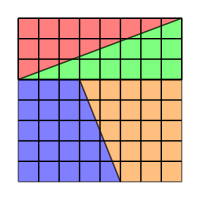

```mathematica
Graphics[{T1,T2,T3,T4},ImageSize->200]
```

```mathematica
(* animation *)
move1[obj_,t_,t1_,t2_]:=
Translate[obj,{5(Min[Max[t,t1],t2]-t1)/(t2-t1),0}];
move2[obj_,t_,t1_,t2_]:=
Translate[obj,{0,-2(Min[Max[t,t1],t2]-t1)/(t2-t1)}];
move3[obj_,t_,t1_,t2_,t3_,t4_]:=
Module[{
tt1=(Min[Max[t,t1],t2]-t1)/(t2-t1),
tt2=(Min[Max[t,t3],t4]-t3)/(t4-t3)
},
Translate[
Rotate[Translate[obj,{-1/2 tt1,4.5 tt1}],-π/2 tt1],
{1/2 tt2,-1.5tt2}
]
]
move4[obj_,t_,t1_,t2_,t3_,t4_]:=
Module[{
tt1=(Min[Max[t,t1],t2]-t1)/(t2-t1),
tt2=(Min[Max[t,t3],t4]-t3)/(t4-t3)
},
Translate[
Rotate[Translate[obj,{5.5tt1,1.5 tt1}],-π/2 tt1],
{-1/2 tt2,1.5tt2}
]
]
```

```mathematica
animation[t_]:={
move1[T1,t,10,15],
move2[T2,t,20,25],
move3[T3,t,30,35,35,40],
move4[T4,t,45,50,50,55]
};
```

```mathematica
Animate[Graphics[
animation[t],
PlotRange->{{-2,15},{-1,10}},
ImageSize->600
],{t,0,80}]
```

```mathematica
Grid[{Map[Graphics,{animation[0],animation[80]}]},ItemSize->{{20,20},Automatic}]
```

-Graphics-

```mathematica
(* transformations T1 and T2 *)
T1[t_,t1_,t2_]:=Module[{tt=(Min[Max[t,t1],t2]-t1)/(t2-t1)},
{Opacity[0.5],Red,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{0,5 - (8/13 5-3)tt},{0,8},{8,8}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{0,i},{8/3(i-5),i}}],{i,6,8}],
Table[Line[{{i,5+3/8 i},{i,8}}],{i,0,7}]
}]
T1[t_,t1_,t2_]={Opacity[0.5],Green,EdgeForm[{Thickness[0.005],Black}],
Polygon[{{0,5},{8,5},{8,8}}],
Opacity[1],Black,Thickness[0.005],
Table[Line[{{8/3(i-5),i},{8,i}}],{i,5,7}],
Table[Line[{{i,5},{i,5+3/8 i}}],{i,0,8}]
};
```

```mathematica
Map
```